## Anharmonic Oscillator

### Initializing

```mathematica
dx=0.04;xmin=-3;xmax=3;xL=Range[xmin,xmax,dx];Lx=Length[xL];
(*Getting the Potential matrix ready*)
Vm=xL^4;

(*Intializing constant-normalized wave function*)
ϕ0=0*xL;
Do[If[xL[[i]]>=-1&&xL[[i]]<=1,ϕ0[[i]]=0.1],{i,Lx}];(*Choosing the constant to be 0.1*)
norm=dx*(ϕ0.ϕ0);
ϕN=ϕ0/Sqrt[norm];(*Normalizing*)

(*Constructing the Hamiltonian matrix (Check Matrix Method Notebook) and Getting Initial Energy*)
(*1. Initializing first and last rows of H*)
Hm=Table[0*xL,{i,1,Lx}];
Hm[[1,1]]=Vm[[1]]+1/(dx)^2;Hm[[1,2]]=-1/(2(dx)^2);Hm[[-1,-1]]=Vm[[-1]]+1/(dx)^2;Hm[[-1,-2]]=-1/(2(dx)^2);
(*2. From the analysis pattern we detect that these are the remaining elements*)
Do[Hm[[i,i]]=Vm[[i]]+1/(dx)^2;Hm[[i,i-1]]=-1/(2(dx)^2);Hm[[i,i+1]]=-1/(2(dx)^2),{i,2,Lx-1}]
(*3. Getting the initial Energy*)
Num=dx*(ϕN.Hm.ϕN);Deno=dx*(ϕN.ϕN);(*Already normalized*)
Es=Num/Deno;
```

### Monte-Carlo Calculations (ALERT: Huge number of steps for better results)

```mathematica
(*Monte-Carlo Coding*)
(*1. Getting random integer to be used as an index.*)
(*2. Getting random increment in range -dx to +dx (Suitable range) to change our function with.*)
(*3. Constructing the new wavefunction and getting the new energy on it.*)
(*4. Comparing old and new energies to check whether to keep ϕN or replace it with ϕnew.*)
(*5. Repeat as many times as possible to get higher accuracy*)
Do[ntest=RandomInteger[{1,Lx}];dϕ=RandomReal[{-dx,dx}];
ϕnew=ϕN;ϕnew[[ntest]]+=dϕ;Enew=(ϕnew.Hm.ϕnew)/(ϕnew.ϕnew);
If[Enew<Es,(ϕN=ϕnew/Sqrt[dx*(ϕnew.ϕnew)])&&(Es=Enew)]
,{h,10^7}]
```

### Extracting results and Plotting

Ground State Energy (Variational): 0.667931

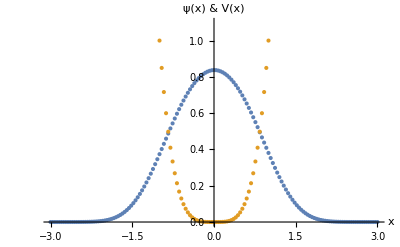

```mathematica
(*Extracting the final results and plotting*)
Print["Ground State Energy (Variational): ",Es]
ϕN=ϕN/Sqrt[dx*(ϕN.ϕN)];(*Normalizing the Final State*)
(*Getting ready to plot*)
potential=Table[{xL[[i]],Vm[[i]]},{i,Lx}];
pairs=Table[{xL[[i]],ϕN[[i]]},{i,Lx}];
ListPlot[{pairs,potential},AxesLabel->{"x","ψ(x) & V(x)"},PlotRange->{All,{0,1.1}}]
(*In agreement with what we got using the matrix method.*)
```